```mathematica
Nftion[x_]:=CDF[NormalDistribution[],x]
```

```mathematica
Nftion[0]
```

1/2

```mathematica
S0=100; r=0.04; σ=0.25; T=1; K=100
```

100

```mathematica
done[s_,t_]:=(Log[s/K]+(r+σ^2/2)*(T-t))/σ/Sqrt[T-t]
```

```mathematica
dtwo[s_,t_]:=done[s,t]-σ*Sqrt[T-t]
```

```mathematica
Call[s_,t_]= s*Nftion[done[s,t]]-K*E^(-r(T-t))*Nftion[dtwo[s,t]]
```

s Nftion[((-t+T) (r+σ^2/2)+Log[s/K])/(√(-t+T) σ)]-ⅇ^(-r (-t+T)) K Nftion[-√(-t+T) σ+((-t+T) (r+σ^2/2)+Log[s/K])/(√(-t+T) σ)]

```mathematica
Call[100,0]
```

11.837

```mathematica
Plot3D[Call[x,y],{x,0,200},{y,0,1}]
```

-Graphics3D-

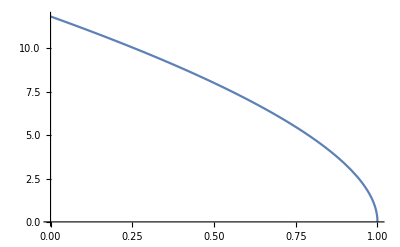

```mathematica
Plot[Call[100,y],{y,0,1}]
```

```mathematica
EuroPut[s_,t_]:= K*E^(-r(T-t))*Nftion[-dtwo[s,t]]-s*Nftion[-done[s,t]]

EuroPut[100,0]
```

7.91599

```mathematica
Plot3D[EuroPut[x,y],{x,0,200},{y,0,1}]
```

-Graphics3D-

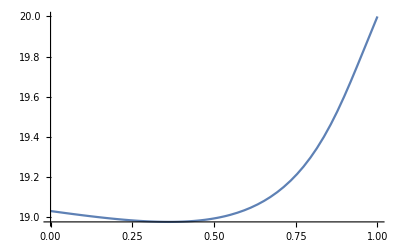

```mathematica
Plot[EuroPut[80,y],{y,0,1}]
```

```mathematica
ΔC[s_,t_]=D[Call[s,t],s]
```

(1.59577 ⅇ^(-(8. (0.07125 (1-t)+Log[s/100])^2)/(1-t)))/(√(1-t))-(159.577 ⅇ^(-0.04 (1-t)-1/2 (0.25 √(1-t)-(4. (0.07125 (1-t)+Log[s/100]))/(√(1-t)))^2))/(s √(1-t))+1/2 Erfc[-(2.82843 (0.07125 (1-t)+Log[s/100]))/(√(1-t))]

```mathematica
Plot3D[ΔC[x,y],{x,0,200},{y,0,1}]
```

```mathematica
ΘC[s_,t_]=D[Call[s,t],t]
```

-2. ⅇ^(-0.04 (1-t)) Erfc[(0.25 √(1-t)-(4. (0.07125 (1-t)+Log[s/100]))/(√(1-t)))/(√2)]+50 ⅇ^(-0.04 (1-t)-1/2 (0.25 √(1-t)-(4. (0.07125 (1-t)+Log[s/100]))/(√(1-t)))^2) √(2/π) (0.16/(√(1-t))-(2. (0.07125 (1-t)+Log[s/100]))/(1-t)^(3/2))-(ⅇ^(-(8. (0.07125 (1-t)+Log[s/100])^2)/(1-t)) s (0.201525/(√(1-t))-(1.41421 (0.07125 (1-t)+Log[s/100]))/(1-t)^(3/2)))/(√π)

```mathematica
Plot3D[ΘC[x,y],{x,0,200},{y,0,1}]
```

-Graphics3D-

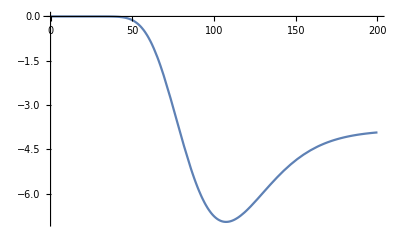

```mathematica
Plot[ΘC[x,0],{x,0,200}]
```

```mathematica
ΘP[s_,t_]=D[EuroPut[s,t],t]
```

2. ⅇ^(-0.04 (1-t)) Erfc[(-0.25 √(1-t)+(4. (0.07125 (1-t)+Log[s/100]))/(√(1-t)))/(√2)]+(ⅇ^(-(8. (0.07125 (1-t)+Log[s/100])^2)/(1-t)) s (-0.201525/(√(1-t))+(1.41421 (0.07125 (1-t)+Log[s/100]))/(1-t)^(3/2)))/(√π)-50 ⅇ^(-0.04 (1-t)-1/2 (-0.25 √(1-t)+(4. (0.07125 (1-t)+Log[s/100]))/(√(1-t)))^2) √(2/π) (-0.16/(√(1-t))+(2. (0.07125 (1-t)+Log[s/100]))/(1-t)^(3/2))

```mathematica
Plot3D[ΘP[x,y],{x,0,200},{y,0,1}]
```

-Graphics3D-

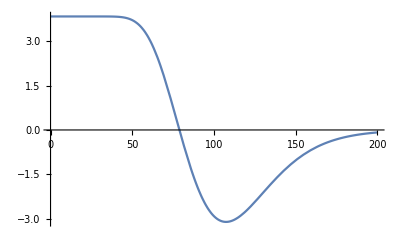

```mathematica
Plot[ΘP[x,0],{x,0,200}]
```

```mathematica
Clear[s,t,σ,r,δ]
```

```mathematica
doneAll[s_,t_,σ_,r_,δ_]= (Log[s/100]+(r-δ+σ^2/2)*(1-t))/σ/Sqrt[1-t]
```

((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ)

```mathematica
dtwoAll[s_,t_, σ_, r_, δ_]= doneAll[s,t,σ,r,δ]-σ*Sqrt[1-t]
```

-√(1-t) σ+((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ)

```mathematica
Together[%]
```

(2 r-2 r t-2 δ+2 t δ-σ^2+t σ^2+2 Log[s/100])/(2 √(1-t) σ)

```mathematica
Simplify[%]
```

(-(-1+t) (2 r-2 δ-σ^2)+2 Log[s/100])/(2 √(1-t) σ)

```mathematica
CallAll[s_,t_,σ_,r_,δ_]= s*E^(-δ*(1-t))*Nftion[doneAll[s,t,σ,r,δ]]-100*E^(-r*(1-t))*Nftion[dtwoAll[s,t,σ,r,δ]]
```

1/2 ⅇ^(-(1-t) δ) s Erfc[-((1-t) (r-δ+σ^2/2)+Log[s/100])/(√2 √(1-t) σ)]-50 ⅇ^(-r (1-t)) Erfc[(√(1-t) σ-((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ))/(√2)]

```mathematica
ΔCallAll[s_,t_,σ_,r_, δ_] = Simplify[D[CallAll[s,t,σ,r,δ],s],Assumptions->{s>0, 0<t, t<1, σ>0}]
```

(ⅇ^(-r-δ) (-100 ⅇ^(r t+δ+(((-1+t) (2 r-2 δ-σ^2)-2 Log[s/100])^2)/(8 (-1+t) σ^2))+ⅇ^(r+t δ+(((-1+t) (2 r-2 δ+σ^2)-2 Log[s/100])^2)/(8 (-1+t) σ^2)) s))/(√(2 π) s √(1-t) σ)+1/2 ⅇ^((-1+t) δ) Erfc[((-1+t) (2 r-2 δ+σ^2)-2 Log[s/100])/(2 √(2-2 t) σ)]

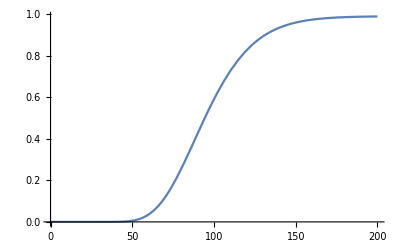

```mathematica
Plot[ΔCallAll[x,0,0.25,0.04,0.01],{x,0,200}]
```

```mathematica
VegaCallAll[s_,t_,σ_,r_,δ_]=D[CallAll[s,t,σ,r,δ],σ]
```

(50 ⅇ^(-r (1-t)-1/2 (√(1-t) σ-((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ))^2) √(2/π) ((1-t) (r-δ+σ^2/2)+Log[s/100]))/(√(1-t) σ^2)-(ⅇ^(-(1-t) δ-(((1-t) (r-δ+σ^2/2)+Log[s/100])^2)/(2 (1-t) σ^2)) s (-(√(1-t))/(√2)+((1-t) (r-δ+σ^2/2)+Log[s/100])/(√2 √(1-t) σ^2)))/(√π)

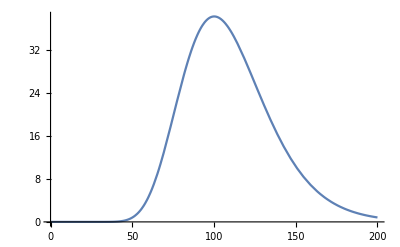

```mathematica
Plot[VegaCallAll[s,0,0.25,0.04,0.01],{s,0,200}]
```

```mathematica
ρCallAll[s_,t_,σ_,r_,δ_]=D[CallAll[s,t,σ,r,δ],r]
```

-(50 ⅇ^(-r (1-t)-1/2 (√(1-t) σ-((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ))^2) √(2/π) √(1-t))/σ+(ⅇ^(-(1-t) δ-(((1-t) (r-δ+σ^2/2)+Log[s/100])^2)/(2 (1-t) σ^2)) s √(1-t))/(√(2 π) σ)-50 ⅇ^(-r (1-t)) (-1+t) Erfc[(√(1-t) σ-((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ))/(√2)]

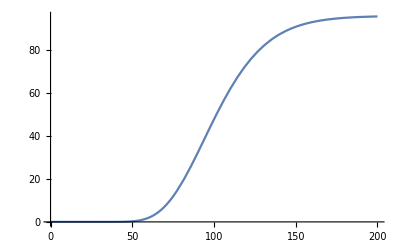

```mathematica
Plot[ρCallAll[s,0,0.25,0.04,0.01],{s,0,200}]
```

```mathematica
ψCallAll[s_,t_,σ_,r_,δ_]=D[CallAll[s,t,σ,r,δ],δ]
```

-(50 ⅇ^(-r (1-t)-1/2 (√(1-t) σ-((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ))^2) √(2/π) (-1+t))/(√(1-t) σ)+(ⅇ^(-(1-t) δ-(((1-t) (r-δ+σ^2/2)+Log[s/100])^2)/(2 (1-t) σ^2)) s (-1+t))/(√(2 π) √(1-t) σ)+1/2 ⅇ^(-(1-t) δ) s (-1+t) Erfc[-((1-t) (r-δ+σ^2/2)+Log[s/100])/(√2 √(1-t) σ)]

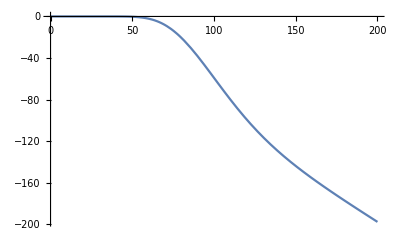

```mathematica
Plot[ψCallAll[s,0,0.25,0.04,0.01],{s,0,200}]
```

```mathematica
PutAll[s_,t_,σ_,r_,δ_]= -s*E^(-δ*(1-t))*Nftion[-doneAll[s,t,σ,r,δ]]+100*E^(-r*(1-t))*Nftion[-dtwoAll[s,t,σ,r,δ]]
```

-1/2 ⅇ^(-(1-t) δ) s Erfc[((1-t) (r-δ+σ^2/2)+Log[s/100])/(√2 √(1-t) σ)]+50 ⅇ^(-r (1-t)) Erfc[(-√(1-t) σ+((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ))/(√2)]

```mathematica
ΔPutAll[s_,t_,σ_,r_, δ_] = D[PutAll[s,t,σ,r,δ],s]
```

(ⅇ^(-(1-t) δ-(((1-t) (r-δ+σ^2/2)+Log[s/100])^2)/(2 (1-t) σ^2)))/(√(2 π) √(1-t) σ)-(50 ⅇ^(-r (1-t)-1/2 (-√(1-t) σ+((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ))^2) √(2/π))/(s √(1-t) σ)-1/2 ⅇ^(-(1-t) δ) Erfc[((1-t) (r-δ+σ^2/2)+Log[s/100])/(√2 √(1-t) σ)]

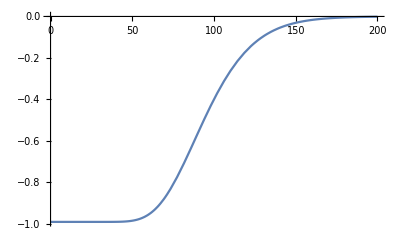

```mathematica
Plot[ΔPutAll[s,0,0.25,0.04,0.01],{s,0,200}]
```

```mathematica
ρPutAll[s_,t_,σ_,r_,δ_]=D[PutAll[s,t,σ,r,δ],r]
```

-(50 ⅇ^(-r (1-t)-1/2 (-√(1-t) σ+((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ))^2) √(2/π) √(1-t))/σ+(ⅇ^(-(1-t) δ-(((1-t) (r-δ+σ^2/2)+Log[s/100])^2)/(2 (1-t) σ^2)) s √(1-t))/(√(2 π) σ)+50 ⅇ^(-r (1-t)) (-1+t) Erfc[(-√(1-t) σ+((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ))/(√2)]

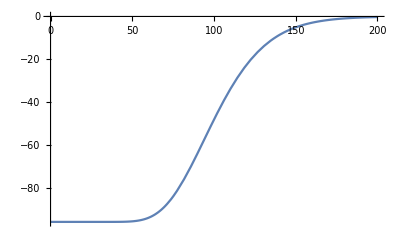

```mathematica
Plot[ρPutAll[s,0,0.25,0.04,0.01],{s,0,200}]
```

```mathematica
ψPutAll[s_,t_,σ_,r_,δ_]=D[PutAll[s,t,σ,r,δ],δ]
```

-(50 ⅇ^(-r (1-t)-1/2 (-√(1-t) σ+((1-t) (r-δ+σ^2/2)+Log[s/100])/(√(1-t) σ))^2) √(2/π) (-1+t))/(√(1-t) σ)+(ⅇ^(-(1-t) δ-(((1-t) (r-δ+σ^2/2)+Log[s/100])^2)/(2 (1-t) σ^2)) s (-1+t))/(√(2 π) √(1-t) σ)-1/2 ⅇ^(-(1-t) δ) s (-1+t) Erfc[((1-t) (r-δ+σ^2/2)+Log[s/100])/(√2 √(1-t) σ)]

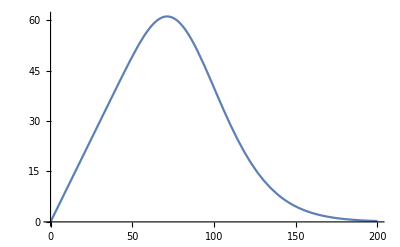

```mathematica
Plot[ψPutAll[s,0,0.25,0.04,0.01],{s,0,200}]
```